At t=0, the displaced medium looks like:

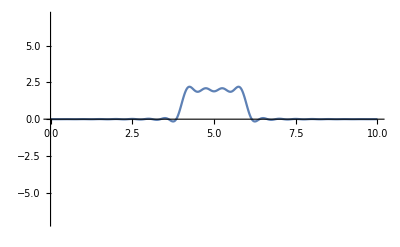

The Spectral Decomposition looks like:

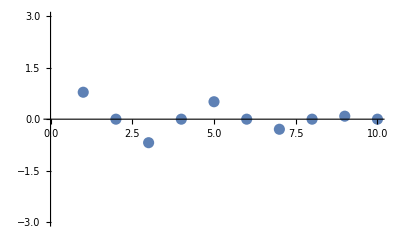

```mathematica
(*Bounded Medium*)
Remove["Global`*"]

(*Reality*)
SetAttributes[{a,f,L}, Constant];
$Assumptions={Element[{a,f,L,x}, Reals]&&Element[n,Integers]&& a>0&&0≤f≤1 && L>0 && 0≤x≤L};

(*Define Initial Shape*)
npieces=3;
F[1][x_]=0;
xlo[1]=0;
xhi[1]=2/5 L;

F[2][x_]=a ;
xlo[2]=xhi[1];
xhi[2]=3/5 L;

F[3][x_]=0;
xlo[3]=xhi[2];
xhi[3]=L;

(*Fourier Coefficients*)
b[n_]= 2/L Sum[Integrate[F[i][x] Sin[n π x/L], {x,xlo[i],xhi[i]}],{i,1,npieces}]//Refine//Simplify;

(*physical perameters*)
L=10;
f=1/3;
a=2;
vx=1;

(*plot parameters*)
nterms=40;
xlow=xlo[1];
xhigh=xhi[npieces];
yrange=7;
range={{xlow,xhigh},{-yrange,yrange}};

(*piece some things back together*)

blist=Table[{n,b[n]},{n,1,nterms}];
wave[x_,t_]=Sum[b[n] Sin[n π x/L] Cos[n π / L vx t], {n,1,nterms}];

(*Display*)
Print["\n At t=0, the displaced medium looks like:"]
Plot[wave[x,0],{x,xlow,xhigh},PlotRange->range]

Print["\nThe Spectral Decomposition looks like:"]
ListPlot[blist, PlotRange->{{0,10},{-3,3}}, PlotStyle->PointSize[0.02]]

waveplot[t_]:=Plot[wave[x,t],{x,xlow,xhigh},PlotRange->range];
Animate[waveplot[t],{t,0,50,.2},DisplayAllSteps->True]
```